### Define Σij=σi@σj

```mathematica
For[i=0,i≤3,i++,For[j=0,j≤3,j++,Σ[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

### Define Hamiltonian with parameters

```mathematica
m=2.5;
t0=1;
t0'=1;
t0''=1;
t=1;
t'=1;
t''=1;
ϕ=0.4;
ϕ2=0.8;
```

```mathematica
Ham[kx_,ky_,kz_]:=(m-t0 Cos[kx]-t0' Cos[ky-ϕ2]-t0'' Cos[kz])Σ[0][3]+t Sin[(kx-ϕ)/2](Sin[kx/2] Σ[1][1]+Cos[kx/2] Σ[2][1])+t' Sin[ky-ϕ2] Σ[0][2]+t'' Sin[kz]Σ[3][1]
```

```mathematica
MatrixForm[Ham[kx,ky,kz]]
```

(2.5-Cos[kx]-Cos[0.8-ky]-Cos[kz] | ⅈ Sin[0.8-ky]+Sin[kz] | 0 | Sin[1/2 (-0.4+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2])
-ⅈ Sin[0.8-ky]+Sin[kz] | -2.5+Cos[kx]+Cos[0.8-ky]+Cos[kz] | Sin[1/2 (-0.4+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2]) | 0
0 | Sin[1/2 (-0.4+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 2.5-Cos[kx]-Cos[0.8-ky]-Cos[kz] | ⅈ Sin[0.8-ky]-Sin[kz]
Sin[1/2 (-0.4+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 0 | -ⅈ Sin[0.8-ky]-Sin[kz] | -2.5+Cos[kx]+Cos[0.8-ky]+Cos[kz])

### Define dispersion function and plot

```mathematica
F[kx_,ky_,kz_]:=Sort[N[Eigenvalues[Ham[kx+0.0,ky+0.0,kz+0.0]]]];
```

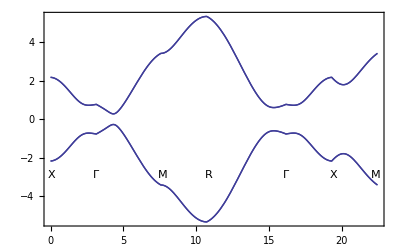

```mathematica
Plot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Find the eigensystem and choose the two lower bands as VEC

```mathematica
ESYS[kx_,ky_,kz_]:=Eigensystem[Ham[kx,ky,kz]]
```

```mathematica
VEC[kx_,ky_,kz_]:=(Clear[VEC1,VEC2];For[i=1;j=1,i≤4,i++,If[ESYS[kx,ky,kz][[1]][[i]]<0,If[j==1,VEC1=ESYS[kx,ky,kz][[2]][[i]];j++,VEC2=ESYS[kx,ky,kz][[2]][[i]]]]];{VEC1,VEC2})
```

```mathematica
VEC[1,1,1]
```

{{-0.0825369+0.151083 ⅈ,0.,0.490206+0.115737 ⅈ,0.84656},{0.501867-0.0427396 ⅈ,-0.837443-0.123909 ⅈ,0.0595343+0.161536 ⅈ,0.}}

#### define numerical integral function

```mathematica
INT[z_,kx_,ky_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.1,int+=0.1z[kx,ky,ii,i,j]]/2/Pi;int)
```

#### define the Core of Correlation function for integral

```mathematica
CORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) kz](KroneckerProduct[Conjugate[VEC[kx,ky,kz][[1]]],VEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[VEC[kx,ky,kz][[2]]],VEC[kx,ky,kz][[2]]])
```

#### define the Correlation function matrix, with 24 by 24

```mathematica
HCOR[kx_,ky_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORE ,kx,ky,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOR[1,1]]]
```

(1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ | 0.720315-5.49249×10^-6 ⅈ | 0.000139377+1.00636 ⅈ | -1.5118×10^-17+6.88256×10^-17 ⅈ | -0.166497-0.304663 ⅈ | 0.154768+0.0000109887 ⅈ | -0.000104996+0.274508 ⅈ | -4.4151×10^-18+4.23052×10^-17 ⅈ | -0.0905663-0.165995 ⅈ | 0.0655683-0.0000164924 ⅈ | 0.0000706888+0.128094 ⅈ | 3.9615×10^-17+4.47395×10^-17 ⅈ | -0.0527809-0.0962931 ⅈ | 0.0342239+0.0000220074 ⅈ | -0.0000364327+0.0675794 ⅈ | 3.17048×10^-17+7.02663×10^-17 ⅈ | -0.0332611-0.0613134 ⅈ | 0.0192588-0.0000275374 ⅈ | 2.205×10^-6+0.0404012 ⅈ | 3.03207×10^-17+4.2094×10^-17 ⅈ | -0.0204346-0.036868 ⅈ
-0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ | 0.000208457+1.47317 ⅈ | -0.737122-0.000693957 ⅈ | -0.166497-0.304663 ⅈ | -3.73182×10^-19+2.4696×10^-19 ⅈ | -0.000243204+0.528752 ⅈ | -0.137984+0.0013884 ⅈ | -0.0905663-0.165995 ⅈ | 7.8795×10^-19-5.57288×10^-19 ⅈ | 0.000278122+0.275737 ⅈ | -0.0823132-0.00208382 ⅈ | -0.0527809-0.0962931 ⅈ | -1.00316×10^-18+1.02848×10^-18 ⅈ | -0.000313237+0.161366 ⅈ | -0.0175334+0.0027807 ⅈ | -0.0332611-0.0613134 ⅈ | 9.66133×10^-19-1.54516×10^-18 ⅈ | 0.000348575+0.0970757 ⅈ | -0.0358789-0.00347955 ⅈ | -0.0204346-0.036868 ⅈ | -6.85923×10^-19+1.98084×10^-18 ⅈ
5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ | 8.89319×10^-17+3.75514×10^-18 ⅈ | -0.166406+0.304712 ⅈ | 0.720315-5.49249×10^-6 ⅈ | -0.000208457-1.47317 ⅈ | 5.09731×10^-17-6.0192×10^-18 ⅈ | -0.0907467+0.165896 ⅈ | 0.154768+0.0000109887 ⅈ | 0.000243204-0.528752 ⅈ | 4.59189×10^-17-3.70542×10^-17 ⅈ | -0.0525102+0.096441 ⅈ | 0.0655683-0.0000164924 ⅈ | -0.000278122-0.275737 ⅈ | 6.27014×10^-17-2.42525×10^-17 ⅈ | -0.0336224+0.061116 ⅈ | 0.0342239+0.0000220074 ⅈ | 0.000313237-0.161366 ⅈ | 1.0749×10^-17+5.58764×10^-18 ⅈ | -0.0199825+0.037115 ⅈ | 0.0192588-0.0000275374 ⅈ | -0.000348575-0.0970757 ⅈ
-0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.166406+0.304712 ⅈ | 6.24823×10^-19-3.54817×10^-19 ⅈ | -0.000139377-1.00636 ⅈ | -0.737122-0.000693957 ⅈ | -0.0907467+0.165896 ⅈ | -9.63713×10^-19+7.46595×10^-19 ⅈ | 0.000104996-0.274508 ⅈ | -0.137984+0.0013884 ⅈ | -0.0525102+0.096441 ⅈ | 1.07329×10^-18-1.25288×10^-18 ⅈ | -0.0000706888-0.128094 ⅈ | -0.0823132-0.00208382 ⅈ | -0.0336224+0.061116 ⅈ | -9.26722×10^-19+1.74973×10^-18 ⅈ | 0.0000364327-0.0675794 ⅈ | -0.0175334+0.0027807 ⅈ | -0.0199825+0.037115 ⅈ | 5.59898×10^-19-2.11548×10^-18 ⅈ | -2.205×10^-6-0.0404012 ⅈ | -0.0358789-0.00347955 ⅈ
0.720315+5.49249×10^-6 ⅈ | 0.000208457-1.47317 ⅈ | 8.89319×10^-17-3.75514×10^-18 ⅈ | -0.166406-0.304712 ⅈ | 1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ | 0.720315-5.49249×10^-6 ⅈ | 0.000139377+1.00636 ⅈ | -1.5118×10^-17+6.88256×10^-17 ⅈ | -0.166497-0.304663 ⅈ | 0.154768+0.0000109887 ⅈ | -0.000104996+0.274508 ⅈ | -4.4151×10^-18+4.23052×10^-17 ⅈ | -0.0905663-0.165995 ⅈ | 0.0655683-0.0000164924 ⅈ | 0.0000706888+0.128094 ⅈ | 3.9615×10^-17+4.47395×10^-17 ⅈ | -0.0527809-0.0962931 ⅈ | 0.0342239+0.0000220074 ⅈ | -0.0000364327+0.0675794 ⅈ | 3.17048×10^-17+7.02663×10^-17 ⅈ | -0.0332611-0.0613134 ⅈ
0.000139377-1.00636 ⅈ | -0.737122+0.000693957 ⅈ | -0.166406-0.304712 ⅈ | 6.24823×10^-19+3.54817×10^-19 ⅈ | -0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ | 0.000208457+1.47317 ⅈ | -0.737122-0.000693957 ⅈ | -0.166497-0.304663 ⅈ | -3.73182×10^-19+2.4696×10^-19 ⅈ | -0.000243204+0.528752 ⅈ | -0.137984+0.0013884 ⅈ | -0.0905663-0.165995 ⅈ | 7.8795×10^-19-5.57288×10^-19 ⅈ | 0.000278122+0.275737 ⅈ | -0.0823132-0.00208382 ⅈ | -0.0527809-0.0962931 ⅈ | -1.00316×10^-18+1.02848×10^-18 ⅈ | -0.000313237+0.161366 ⅈ | -0.0175334+0.0027807 ⅈ | -0.0332611-0.0613134 ⅈ | 9.66133×10^-19-1.54516×10^-18 ⅈ
-1.5118×10^-17-6.88256×10^-17 ⅈ | -0.166497+0.304663 ⅈ | 0.720315+5.49249×10^-6 ⅈ | -0.000139377+1.00636 ⅈ | 5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ | 8.89319×10^-17+3.75514×10^-18 ⅈ | -0.166406+0.304712 ⅈ | 0.720315-5.49249×10^-6 ⅈ | -0.000208457-1.47317 ⅈ | 5.09731×10^-17-6.0192×10^-18 ⅈ | -0.0907467+0.165896 ⅈ | 0.154768+0.0000109887 ⅈ | 0.000243204-0.528752 ⅈ | 4.59189×10^-17-3.70542×10^-17 ⅈ | -0.0525102+0.096441 ⅈ | 0.0655683-0.0000164924 ⅈ | -0.000278122-0.275737 ⅈ | 6.27014×10^-17-2.42525×10^-17 ⅈ | -0.0336224+0.061116 ⅈ | 0.0342239+0.0000220074 ⅈ | 0.000313237-0.161366 ⅈ
-0.166497+0.304663 ⅈ | -3.73182×10^-19-2.4696×10^-19 ⅈ | -0.000208457+1.47317 ⅈ | -0.737122+0.000693957 ⅈ | -0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.166406+0.304712 ⅈ | 6.24823×10^-19-3.54817×10^-19 ⅈ | -0.000139377-1.00636 ⅈ | -0.737122-0.000693957 ⅈ | -0.0907467+0.165896 ⅈ | -9.63713×10^-19+7.46595×10^-19 ⅈ | 0.000104996-0.274508 ⅈ | -0.137984+0.0013884 ⅈ | -0.0525102+0.096441 ⅈ | 1.07329×10^-18-1.25288×10^-18 ⅈ | -0.0000706888-0.128094 ⅈ | -0.0823132-0.00208382 ⅈ | -0.0336224+0.061116 ⅈ | -9.26722×10^-19+1.74973×10^-18 ⅈ | 0.0000364327-0.0675794 ⅈ | -0.0175334+0.0027807 ⅈ
0.154768-0.0000109887 ⅈ | -0.000243204-0.528752 ⅈ | 5.09731×10^-17+6.0192×10^-18 ⅈ | -0.0907467-0.165896 ⅈ | 0.720315+5.49249×10^-6 ⅈ | 0.000208457-1.47317 ⅈ | 8.89319×10^-17-3.75514×10^-18 ⅈ | -0.166406-0.304712 ⅈ | 1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ | 0.720315-5.49249×10^-6 ⅈ | 0.000139377+1.00636 ⅈ | -1.5118×10^-17+6.88256×10^-17 ⅈ | -0.166497-0.304663 ⅈ | 0.154768+0.0000109887 ⅈ | -0.000104996+0.274508 ⅈ | -4.4151×10^-18+4.23052×10^-17 ⅈ | -0.0905663-0.165995 ⅈ | 0.0655683-0.0000164924 ⅈ | 0.0000706888+0.128094 ⅈ | 3.9615×10^-17+4.47395×10^-17 ⅈ | -0.0527809-0.0962931 ⅈ
-0.000104996-0.274508 ⅈ | -0.137984-0.0013884 ⅈ | -0.0907467-0.165896 ⅈ | -9.63713×10^-19-7.46595×10^-19 ⅈ | 0.000139377-1.00636 ⅈ | -0.737122+0.000693957 ⅈ | -0.166406-0.304712 ⅈ | 6.24823×10^-19+3.54817×10^-19 ⅈ | -0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ | 0.000208457+1.47317 ⅈ | -0.737122-0.000693957 ⅈ | -0.166497-0.304663 ⅈ | -3.73182×10^-19+2.4696×10^-19 ⅈ | -0.000243204+0.528752 ⅈ | -0.137984+0.0013884 ⅈ | -0.0905663-0.165995 ⅈ | 7.8795×10^-19-5.57288×10^-19 ⅈ | 0.000278122+0.275737 ⅈ | -0.0823132-0.00208382 ⅈ | -0.0527809-0.0962931 ⅈ | -1.00316×10^-18+1.02848×10^-18 ⅈ
-4.4151×10^-18-4.23052×10^-17 ⅈ | -0.0905663+0.165995 ⅈ | 0.154768-0.0000109887 ⅈ | 0.000104996+0.274508 ⅈ | -1.5118×10^-17-6.88256×10^-17 ⅈ | -0.166497+0.304663 ⅈ | 0.720315+5.49249×10^-6 ⅈ | -0.000139377+1.00636 ⅈ | 5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ | 8.89319×10^-17+3.75514×10^-18 ⅈ | -0.166406+0.304712 ⅈ | 0.720315-5.49249×10^-6 ⅈ | -0.000208457-1.47317 ⅈ | 5.09731×10^-17-6.0192×10^-18 ⅈ | -0.0907467+0.165896 ⅈ | 0.154768+0.0000109887 ⅈ | 0.000243204-0.528752 ⅈ | 4.59189×10^-17-3.70542×10^-17 ⅈ | -0.0525102+0.096441 ⅈ | 0.0655683-0.0000164924 ⅈ | -0.000278122-0.275737 ⅈ
-0.0905663+0.165995 ⅈ | 7.8795×10^-19+5.57288×10^-19 ⅈ | 0.000243204+0.528752 ⅈ | -0.137984-0.0013884 ⅈ | -0.166497+0.304663 ⅈ | -3.73182×10^-19-2.4696×10^-19 ⅈ | -0.000208457+1.47317 ⅈ | -0.737122+0.000693957 ⅈ | -0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.166406+0.304712 ⅈ | 6.24823×10^-19-3.54817×10^-19 ⅈ | -0.000139377-1.00636 ⅈ | -0.737122-0.000693957 ⅈ | -0.0907467+0.165896 ⅈ | -9.63713×10^-19+7.46595×10^-19 ⅈ | 0.000104996-0.274508 ⅈ | -0.137984+0.0013884 ⅈ | -0.0525102+0.096441 ⅈ | 1.07329×10^-18-1.25288×10^-18 ⅈ | -0.0000706888-0.128094 ⅈ | -0.0823132-0.00208382 ⅈ
0.0655683+0.0000164924 ⅈ | 0.000278122-0.275737 ⅈ | 4.59189×10^-17+3.70542×10^-17 ⅈ | -0.0525102-0.096441 ⅈ | 0.154768-0.0000109887 ⅈ | -0.000243204-0.528752 ⅈ | 5.09731×10^-17+6.0192×10^-18 ⅈ | -0.0907467-0.165896 ⅈ | 0.720315+5.49249×10^-6 ⅈ | 0.000208457-1.47317 ⅈ | 8.89319×10^-17-3.75514×10^-18 ⅈ | -0.166406-0.304712 ⅈ | 1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ | 0.720315-5.49249×10^-6 ⅈ | 0.000139377+1.00636 ⅈ | -1.5118×10^-17+6.88256×10^-17 ⅈ | -0.166497-0.304663 ⅈ | 0.154768+0.0000109887 ⅈ | -0.000104996+0.274508 ⅈ | -4.4151×10^-18+4.23052×10^-17 ⅈ | -0.0905663-0.165995 ⅈ
0.0000706888-0.128094 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0525102-0.096441 ⅈ | 1.07329×10^-18+1.25288×10^-18 ⅈ | -0.000104996-0.274508 ⅈ | -0.137984-0.0013884 ⅈ | -0.0907467-0.165896 ⅈ | -9.63713×10^-19-7.46595×10^-19 ⅈ | 0.000139377-1.00636 ⅈ | -0.737122+0.000693957 ⅈ | -0.166406-0.304712 ⅈ | 6.24823×10^-19+3.54817×10^-19 ⅈ | -0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ | 0.000208457+1.47317 ⅈ | -0.737122-0.000693957 ⅈ | -0.166497-0.304663 ⅈ | -3.73182×10^-19+2.4696×10^-19 ⅈ | -0.000243204+0.528752 ⅈ | -0.137984+0.0013884 ⅈ | -0.0905663-0.165995 ⅈ | 7.8795×10^-19-5.57288×10^-19 ⅈ
3.9615×10^-17-4.47395×10^-17 ⅈ | -0.0527809+0.0962931 ⅈ | 0.0655683+0.0000164924 ⅈ | -0.0000706888+0.128094 ⅈ | -4.4151×10^-18-4.23052×10^-17 ⅈ | -0.0905663+0.165995 ⅈ | 0.154768-0.0000109887 ⅈ | 0.000104996+0.274508 ⅈ | -1.5118×10^-17-6.88256×10^-17 ⅈ | -0.166497+0.304663 ⅈ | 0.720315+5.49249×10^-6 ⅈ | -0.000139377+1.00636 ⅈ | 5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ | 8.89319×10^-17+3.75514×10^-18 ⅈ | -0.166406+0.304712 ⅈ | 0.720315-5.49249×10^-6 ⅈ | -0.000208457-1.47317 ⅈ | 5.09731×10^-17-6.0192×10^-18 ⅈ | -0.0907467+0.165896 ⅈ | 0.154768+0.0000109887 ⅈ | 0.000243204-0.528752 ⅈ
-0.0527809+0.0962931 ⅈ | -1.00316×10^-18-1.02848×10^-18 ⅈ | -0.000278122+0.275737 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0905663+0.165995 ⅈ | 7.8795×10^-19+5.57288×10^-19 ⅈ | 0.000243204+0.528752 ⅈ | -0.137984-0.0013884 ⅈ | -0.166497+0.304663 ⅈ | -3.73182×10^-19-2.4696×10^-19 ⅈ | -0.000208457+1.47317 ⅈ | -0.737122+0.000693957 ⅈ | -0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.166406+0.304712 ⅈ | 6.24823×10^-19-3.54817×10^-19 ⅈ | -0.000139377-1.00636 ⅈ | -0.737122-0.000693957 ⅈ | -0.0907467+0.165896 ⅈ | -9.63713×10^-19+7.46595×10^-19 ⅈ | 0.000104996-0.274508 ⅈ | -0.137984+0.0013884 ⅈ
0.0342239-0.0000220074 ⅈ | -0.000313237-0.161366 ⅈ | 6.27014×10^-17+2.42525×10^-17 ⅈ | -0.0336224-0.061116 ⅈ | 0.0655683+0.0000164924 ⅈ | 0.000278122-0.275737 ⅈ | 4.59189×10^-17+3.70542×10^-17 ⅈ | -0.0525102-0.096441 ⅈ | 0.154768-0.0000109887 ⅈ | -0.000243204-0.528752 ⅈ | 5.09731×10^-17+6.0192×10^-18 ⅈ | -0.0907467-0.165896 ⅈ | 0.720315+5.49249×10^-6 ⅈ | 0.000208457-1.47317 ⅈ | 8.89319×10^-17-3.75514×10^-18 ⅈ | -0.166406-0.304712 ⅈ | 1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ | 0.720315-5.49249×10^-6 ⅈ | 0.000139377+1.00636 ⅈ | -1.5118×10^-17+6.88256×10^-17 ⅈ | -0.166497-0.304663 ⅈ
-0.0000364327-0.0675794 ⅈ | -0.0175334-0.0027807 ⅈ | -0.0336224-0.061116 ⅈ | -9.26722×10^-19-1.74973×10^-18 ⅈ | 0.0000706888-0.128094 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0525102-0.096441 ⅈ | 1.07329×10^-18+1.25288×10^-18 ⅈ | -0.000104996-0.274508 ⅈ | -0.137984-0.0013884 ⅈ | -0.0907467-0.165896 ⅈ | -9.63713×10^-19-7.46595×10^-19 ⅈ | 0.000139377-1.00636 ⅈ | -0.737122+0.000693957 ⅈ | -0.166406-0.304712 ⅈ | 6.24823×10^-19+3.54817×10^-19 ⅈ | -0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ | 0.000208457+1.47317 ⅈ | -0.737122-0.000693957 ⅈ | -0.166497-0.304663 ⅈ | -3.73182×10^-19+2.4696×10^-19 ⅈ
3.17048×10^-17-7.02663×10^-17 ⅈ | -0.0332611+0.0613134 ⅈ | 0.0342239-0.0000220074 ⅈ | 0.0000364327+0.0675794 ⅈ | 3.9615×10^-17-4.47395×10^-17 ⅈ | -0.0527809+0.0962931 ⅈ | 0.0655683+0.0000164924 ⅈ | -0.0000706888+0.128094 ⅈ | -4.4151×10^-18-4.23052×10^-17 ⅈ | -0.0905663+0.165995 ⅈ | 0.154768-0.0000109887 ⅈ | 0.000104996+0.274508 ⅈ | -1.5118×10^-17-6.88256×10^-17 ⅈ | -0.166497+0.304663 ⅈ | 0.720315+5.49249×10^-6 ⅈ | -0.000139377+1.00636 ⅈ | 5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ | 8.89319×10^-17+3.75514×10^-18 ⅈ | -0.166406+0.304712 ⅈ | 0.720315-5.49249×10^-6 ⅈ | -0.000208457-1.47317 ⅈ
-0.0332611+0.0613134 ⅈ | 9.66133×10^-19+1.54516×10^-18 ⅈ | 0.000313237+0.161366 ⅈ | -0.0175334-0.0027807 ⅈ | -0.0527809+0.0962931 ⅈ | -1.00316×10^-18-1.02848×10^-18 ⅈ | -0.000278122+0.275737 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0905663+0.165995 ⅈ | 7.8795×10^-19+5.57288×10^-19 ⅈ | 0.000243204+0.528752 ⅈ | -0.137984-0.0013884 ⅈ | -0.166497+0.304663 ⅈ | -3.73182×10^-19-2.4696×10^-19 ⅈ | -0.000208457+1.47317 ⅈ | -0.737122+0.000693957 ⅈ | -0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.166406+0.304712 ⅈ | 6.24823×10^-19-3.54817×10^-19 ⅈ | -0.000139377-1.00636 ⅈ | -0.737122-0.000693957 ⅈ
0.0192588+0.0000275374 ⅈ | 0.000348575-0.0970757 ⅈ | 1.0749×10^-17-5.58764×10^-18 ⅈ | -0.0199825-0.037115 ⅈ | 0.0342239-0.0000220074 ⅈ | -0.000313237-0.161366 ⅈ | 6.27014×10^-17+2.42525×10^-17 ⅈ | -0.0336224-0.061116 ⅈ | 0.0655683+0.0000164924 ⅈ | 0.000278122-0.275737 ⅈ | 4.59189×10^-17+3.70542×10^-17 ⅈ | -0.0525102-0.096441 ⅈ | 0.154768-0.0000109887 ⅈ | -0.000243204-0.528752 ⅈ | 5.09731×10^-17+6.0192×10^-18 ⅈ | -0.0907467-0.165896 ⅈ | 0.720315+5.49249×10^-6 ⅈ | 0.000208457-1.47317 ⅈ | 8.89319×10^-17-3.75514×10^-18 ⅈ | -0.166406-0.304712 ⅈ | 1.26899+0. ⅈ | -0.000173856-0.619727 ⅈ | 5.54461×10^-17+4.84422×10^-17 ⅈ | -0.441955-0.808993 ⅈ
2.205×10^-6-0.0404012 ⅈ | -0.0358789+0.00347955 ⅈ | -0.0199825-0.037115 ⅈ | 5.59898×10^-19+2.11548×10^-18 ⅈ | -0.0000364327-0.0675794 ⅈ | -0.0175334-0.0027807 ⅈ | -0.0336224-0.061116 ⅈ | -9.26722×10^-19-1.74973×10^-18 ⅈ | 0.0000706888-0.128094 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0525102-0.096441 ⅈ | 1.07329×10^-18+1.25288×10^-18 ⅈ | -0.000104996-0.274508 ⅈ | -0.137984-0.0013884 ⅈ | -0.0907467-0.165896 ⅈ | -9.63713×10^-19-7.46595×10^-19 ⅈ | 0.000139377-1.00636 ⅈ | -0.737122+0.000693957 ⅈ | -0.166406-0.304712 ⅈ | 6.24823×10^-19+3.54817×10^-19 ⅈ | -0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ | -0.441955-0.808993 ⅈ | -1.39591×10^-19-1.73472×10^-19 ⅈ
3.03207×10^-17-4.2094×10^-17 ⅈ | -0.0204346+0.036868 ⅈ | 0.0192588+0.0000275374 ⅈ | -2.205×10^-6+0.0404012 ⅈ | 3.17048×10^-17-7.02663×10^-17 ⅈ | -0.0332611+0.0613134 ⅈ | 0.0342239-0.0000220074 ⅈ | 0.0000364327+0.0675794 ⅈ | 3.9615×10^-17-4.47395×10^-17 ⅈ | -0.0527809+0.0962931 ⅈ | 0.0655683+0.0000164924 ⅈ | -0.0000706888+0.128094 ⅈ | -4.4151×10^-18-4.23052×10^-17 ⅈ | -0.0905663+0.165995 ⅈ | 0.154768-0.0000109887 ⅈ | 0.000104996+0.274508 ⅈ | -1.5118×10^-17-6.88256×10^-17 ⅈ | -0.166497+0.304663 ⅈ | 0.720315+5.49249×10^-6 ⅈ | -0.000139377+1.00636 ⅈ | 5.54461×10^-17-4.84422×10^-17 ⅈ | -0.441955+0.808993 ⅈ | 1.26899+0. ⅈ | 0.000173856-0.619727 ⅈ
-0.0204346+0.036868 ⅈ | -6.85923×10^-19-1.98084×10^-18 ⅈ | -0.000348575+0.0970757 ⅈ | -0.0358789+0.00347955 ⅈ | -0.0332611+0.0613134 ⅈ | 9.66133×10^-19+1.54516×10^-18 ⅈ | 0.000313237+0.161366 ⅈ | -0.0175334-0.0027807 ⅈ | -0.0527809+0.0962931 ⅈ | -1.00316×10^-18-1.02848×10^-18 ⅈ | -0.000278122+0.275737 ⅈ | -0.0823132+0.00208382 ⅈ | -0.0905663+0.165995 ⅈ | 7.8795×10^-19+5.57288×10^-19 ⅈ | 0.000243204+0.528752 ⅈ | -0.137984-0.0013884 ⅈ | -0.166497+0.304663 ⅈ | -3.73182×10^-19-2.4696×10^-19 ⅈ | -0.000208457+1.47317 ⅈ | -0.737122+0.000693957 ⅈ | -0.441955+0.808993 ⅈ | -1.39591×10^-19+1.73472×10^-19 ⅈ | 0.000173856+0.619727 ⅈ | 5.03101+0. ⅈ)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
FCOR[kx_,ky_]:=Sort[Eigenvalues[HCOR[kx,ky]]]
```

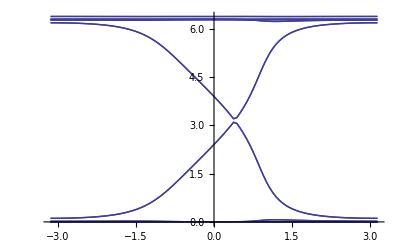

```mathematica
DiscretePlot[FCOR[T,0.8],{T,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True]]
```

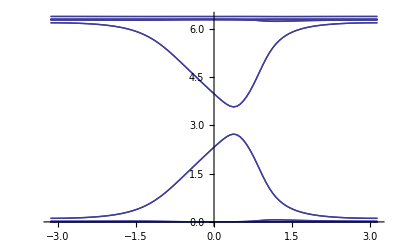

```mathematica
DiscretePlot[FCOR[T,0.9],{T,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True]]
```

```mathematica
DiscretePlot[FCOR[T,0.7],{T,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True]]
```

-Graphics-

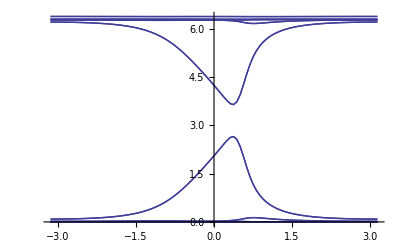

```mathematica
DiscretePlot[FCOR[T,0.75],{T,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True]]
```

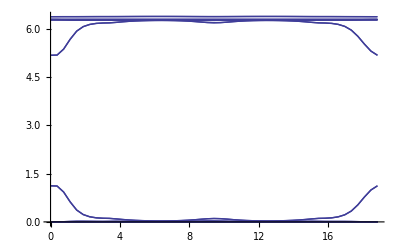

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<4Pi},{FCOR[-Pi,5Pi-T],T≥4Pi&&T≤5Pi},{FCOR[-6Pi+T,0],T≥5Pi&&T≤6Pi}}],{T,0,6Pi,6Pi/50},Filling->None,Evaluate[Joined->True]]
```

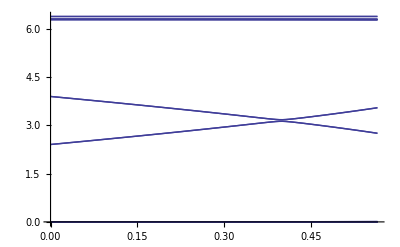

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{FCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,0.18Pi,0.18Pi/100},Filling->None,Evaluate[Joined->True]]
```

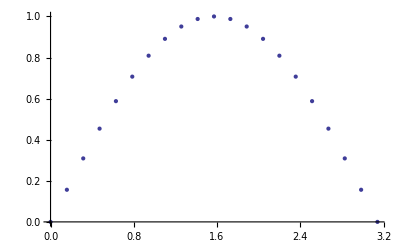

```mathematica
DiscretePlot[Sin[x],{x,0,Pi,Pi/20},Filling->None]
```

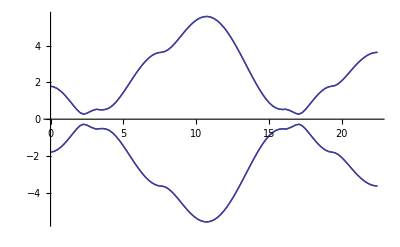

```mathematica
DiscretePlot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi,(4+Sqrt[2]+Sqrt[3])Pi/100},Filling->None,Evaluate[Joined->True]]
```